## Brain Haemorrhage Diagnosis - Using Lenet based Deep Learning Model

```mathematica
(*change the path to the data source in your pc*)
```

```mathematica
infected=FileNames["*.png","E:\\COURSES\\Wolfram\\Brain Tumor Images Dataset\\training_set\\hemmorhage_data"];
uninfected=FileNames["*.png","E:\\COURSES\\Wolfram\\Brain Tumor Images Dataset\\training_set\\non_hemmorhage_data"];
```

```mathematica
infectedIMG=File/@infected;
uninfectedIMG=File/@uninfected;
```

```mathematica
Length[infectedIMG]
```

70

```mathematica
infectedvalues=Table[True,Length[infected]];
Length[uninfected]
```

70

```mathematica
uninfectedvalues = Table[False, Length[uninfected]];
```

```mathematica
data = RandomSample[AssociationThread[infectedIMG -> infectedvalues]];
traininglength = Length[data]*.75
```

52.5

```mathematica
trainingdata=data[[1;;52]];
validationdata=data[[53;;]];
```

```mathematica
dims={135,135}
```

{135,135}

```mathematica
lenet=NetChain[{ResizeLayer[dims],ConvolutionLayer[20,5],Ramp,(*Takes out the the not useful features*)PoolingLayer[2,2],(*Downsamples*)ConvolutionLayer[50,5],Ramp,(*Takes out the the not useful features*)PoolingLayer[2,2],(*Downsamples*)FlattenLayer[],500,(*Makes features into feature vector"*)Ramp,2,(*Takes out the the not useful features-True or false*)SoftmaxLayer[]},(*Turns the vector into probabilities*)"Output"->NetDecoder[{"Class",{True,False}}],(*Tensor into true or false*)"Input"->NetEncoder["Image"](*Turns image into numbers*)]
```

NetChain[<>]

```mathematica
results = 
 NetTrain[lenet, Normal[trainingdata], All, 
  ValidationSet -> Normal[validationdata], MaxTrainingRounds -> 10, 
  TargetDevice -> "CPU"]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10  rounds:10  time:25s  examples/s:21.
data | ,,  training examples:52  validation examples:18  processed examples:520  skipped examples:0
method | ,,  ADAMoptimizer  batch size52CPU
round | ,,  loss:0.  error:0%
validation | ,,  loss:0.  error:0%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
augment=ImageAugmentationLayer[{135,135},"Input"->NetEncoder[{"Image",{139,139}}],"Output"->NetDecoder["Image"]]
```

ImageAugmentationLayer[<>]

```mathematica
dims2={139,139}

lenet2=NetChain[{ResizeLayer[dims2],ImageAugmentationLayer[{135,135}],ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,2,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{True,False}}],"Input"->NetEncoder["Image"]]
```

{139,139}

NetChain[<>]

```mathematica
results2 = 
 NetTrain[lenet2, Normal[trainingdata], All, 
  ValidationSet -> Normal[validationdata], MaxTrainingRounds -> 7]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:91  rounds:7  time:31s  examples/s:12.
data | ,,  training examples:52  validation examples:18  processed examples:364  skipped examples:0
method | ,,  ADAMoptimizer  batch size4CPU
round | ,,  loss:0.  error:0%
validation | ,,  loss:0.  error:0%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trained = results2["TrainedNet"]
```

NetChain[<>]

```mathematica
Export["augmentnet.wlnet",trained]
```

augmentnet.wlnet

```mathematica
trained2 = results["TrainedNet"]
```

NetChain[<>]

```mathematica
trained = Import["E:\\COURSES\\Wolfram\\Projects\\augmentnet.wlnet"]
```

NetChain[<>]

```mathematica
WLNetImport[E:\\COURSES\\Wolfram\\Projects\\augmentnet.wlnet,Net]
```

```mathematica
testset = Import/@Keys[validationdata];
```

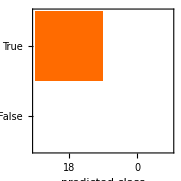
Classifier Measurements
Classifier method | Net
Number of test examples | 18
Accuracy | (100.00000000000000022) %
Accuracy baseline | (100.00000000000000022) %
Single evaluation time | 31.1 ms/example
Batch evaluation speed | 11.4 examples/s
-Graphics- |

```mathematica
visual= ClassifierMeasurements[trained,Normal[RandomSample[AssociationThread[testset->Values[validationdata]]]]]
```

```mathematica
visual/@{"Accuracy","FScore","ConfusionMatrixPlot","Precision","Recall","Sensitivity","FalsePositiveRate","WorstClassifiedExamples"}//TableForm
```

1. |  |  |  |  |  |  |  |  | 
<|True→1.,False→Indeterminate|> |  |  |  |  |  |  |  |  | 
-Graphics- |  |  |  |  |  |  |  |  | 
<|True→1.,False→Indeterminate|> |  |  |  |  |  |  |  |  | 
<|True→1.,False→Indeterminate|> |  |  |  |  |  |  |  |  | 
<|True→1.,False→Indeterminate|> |  |  |  |  |  |  |  |  | 
<|True→Indeterminate,False→0.|> |  |  |  |  |  |  |  |  | 
-Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True